# Code to check C_3 symmetry criterion for Chern band in Haldane model :

References : 
 
 1. Fang, C ., Gilbert, M . J . & Bernevig, B . A . Bulk topological invariants in noninteracting point group symmetric insulators . Phys . Rev . B 86, 115112 (2012) .
  2.  Bultinck, N . et al . Ground State and Hidden Symmetry of Magic - Angle Graphene at even Integer Filling . Physical Review X 10, (2020) .
  3. Vanderbilt D . Berry Phases in Electronic Structure Theory : Electric Polarization, Orbital Magnetization and Topological Insulators . Cambridge University Press, 2018.

## Lattice definitions

```mathematica
a1 = {1,0};
a2 = RotationMatrix[2π/3].a1;
a3 = RotationMatrix[2π/3].a2;
```

```mathematica
R1 = a2 - a1;
R2 = a1 - a3;
```

```mathematica
Rcut = 20;
```

```mathematica
LatA = Select[Flatten[Table[n R1 + m R2,{m,-30,30},{n,-30,30}],1],Norm[#]<Rcut&];
LatB =Select[ Flatten[Table[n R1 + m R2 + a1,{m,-30,30},{n,-30,30}],1],Norm[#]<Rcut&];
```

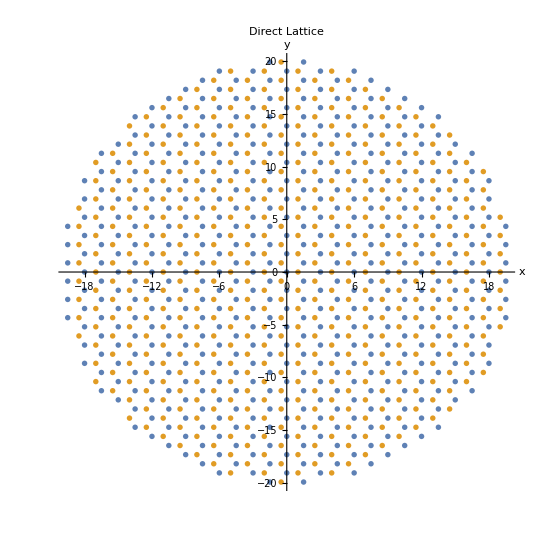

```mathematica
ListPlot[{LatA,LatB},AspectRatio->1,PlotLabel->"Direct Lattice",AxesLabel->{"x","y"},BaseStyle->16]
```

```mathematica
R1
R2
```

{-3/2,(√3)/2}

{3/2,(√3)/2}

```mathematica
b2= (4π)/(3 √3){-(√3)/2,3/2};
b1 = (4π)/(3 √3){(√3)/2,3/2};
```

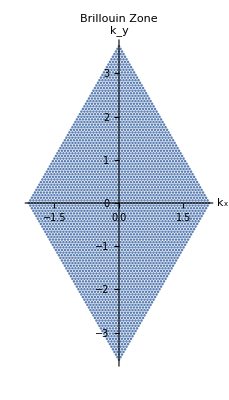

```mathematica
N1 = 60;N2 = 60;
BZ = Flatten[Table[m/N1 b1 + n/N1 b2,{m,-N1/2,N1/2},{n,-N2/2,N2/2}],1];
ListPlot[BZ,AspectRatio->Full,PlotLabel->"Brillouin Zone",AxesLabel->{"k_x","k_y"},BaseStyle->16]
```

```mathematica
t1=1;
t2 =0.01;
Δ = 0;
f[k_]:=t1( Exp[ⅈ k.a1]+ Exp[ⅈ k.a2] + Exp[ⅈ k.a3])//N;
g[k_]:= - 2t2 (Sin[k.R1]+Sin[k.RotationMatrix[2π/3].R1]+Sin[k.RotationMatrix[4π/3].R1])
```

```mathematica
H[k_]:={{Δ+g[k],f[k]},{Conjugate[f[k]],-Δ-g[k]}}
```

```mathematica
ListPlot3D[{Table[{BZ[[i,1]],BZ[[i,2]],Sort[Eigenvalues[H[BZ[[i]]]]][[1]]},{i,1,Length[BZ]}],Table[{BZ[[i,1]],BZ[[i,2]],Sort[Eigenvalues[H[BZ[[i]]]]][[2]]},{i,1,Length[BZ]}]},AspectRatio->1,PlotLegends->Automatic,PlotLabel->"Energy dispersion of Haldane model with Δ = "<>ToString[Δ]<>", t_1 = " <> ToString[t1]<>", t_2 = "<>ToString[t2],AxesLabel->{"k_x","k_y","E(k_x,k_y)"},BaseStyle->16,ImageSize->Large]
```

-Graphics3D-

### Berry curvature and Chern number

```mathematica
Berry[ψ0_]:=-Table[Log[(Conjugate[ψ0[[i,j]]].ψ0[[i,j+1]]/Abs[Conjugate[ψ0[[i,j]]].ψ0[[i,j+1]]])(Conjugate[ψ0[[i,j+1]]].ψ0[[i+1,j+1]]/Abs[Conjugate[ψ0[[i,j+1]]].ψ0[[i+1,j+1]]])(Abs[Conjugate[ψ0[[i+1,j]]].ψ0[[i+1,j+1]]]/Conjugate[ψ0[[i+1,j]]].ψ0[[i+1,j+1]])(Abs[Conjugate[ψ0[[i,j]]].ψ0[[i+1,j]]]/Conjugate[ψ0[[i,j]]].ψ0[[i+1,j]])],{i,1,Length[ψ0]-1},{j,1,Length[ψ0[[1]]]-1}] (*minus sign added because the direction of integral is not counter clockwise for chosen reciprocal basis vectors *)
```

```mathematica
psi1 = Table[Transpose[SortBy[Transpose[Eigensystem[H[m/N1 b1 + n/N2 b2]]],First]][[2,1]],{m,-N1/2,N1/2},{n,-N2/2,N2/2}];psi2=Table[Transpose[SortBy[Transpose[Eigensystem[H[m/N1 b1 + n/N2 b2]]],First]][[2,2]],{m,-N1/2,N1/2},{n,-N2/2,N2/2}];
```

```mathematica
b1
b2
```

{(2 π)/3,(2 π)/(√3)}

{-(2 π)/3,(2 π)/(√3)}

```mathematica
psi1//Dimensions
```

{61,61,2}

```mathematica
bercurv1 = Berry[psi1]//Chop;
bercurv2= Berry[psi2]//Chop;
```

```mathematica
gamma1=1/(2π ⅈ)Sum[Flatten[bercurv1][[i]],{i,1,Length[Flatten[bercurv1]]}]//Chop
gamma2 = 1/(2π ⅈ)Sum[Flatten[bercurv2][[i]],{i,1,Length[Flatten[bercurv1]]}]//Chop
```

-1.

1.

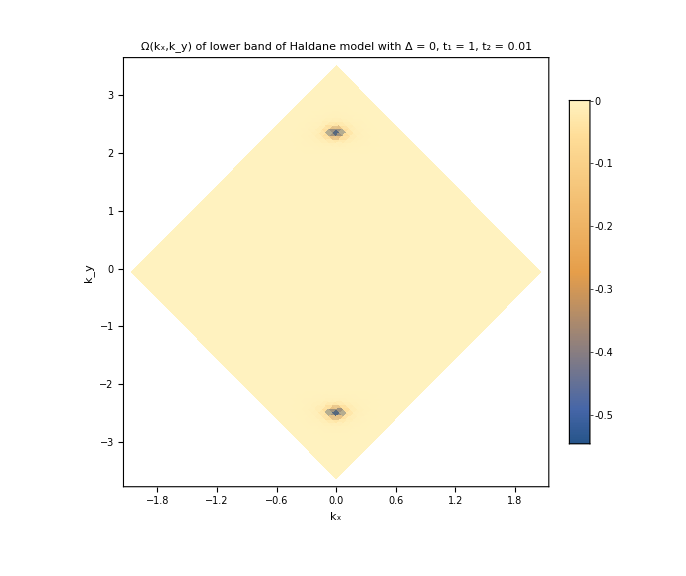

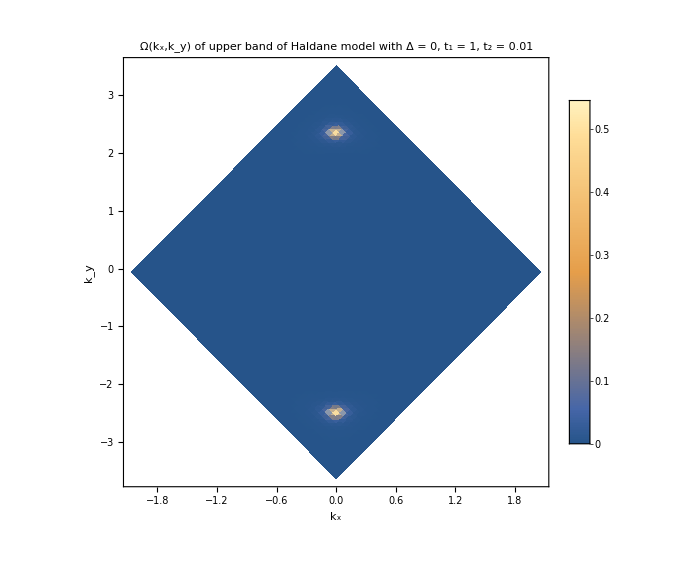

```mathematica
bz = Table[m/N1 b1 + n/N2 b2,{m,-N1/2,N1/2},{n,-N2/2,N2/2}]//N;
ListDensityPlot[Flatten[Table[{ bz[[i,j]][[1]], bz[[i,j]][[2]],Chop[Im[bercurv1[[i,j]]]]},{i,1,Length[bercurv]},{j,1,Length[bercurv]}],1],PlotLegends->Automatic,PlotRange->All,PlotLabel->"Ω(k_x,k_y) of lower band of Haldane model with Δ = "<>ToString[Δ]<>", t_1 = " <> ToString[t1]<>", t_2 = "<>ToString[t2],FrameLabel->{"k_x","k_y"},BaseStyle->16,ImageSize->Large]
ListDensityPlot[Flatten[Table[{ bz[[i,j]][[1]], bz[[i,j]][[2]],Chop[Im[bercurv2[[i,j]]]]},{i,1,Length[bercurv]},{j,1,Length[bercurv]}],1],PlotLegends->Automatic,PlotRange->All,PlotLabel->"Ω(k_x,k_y) of upper band of Haldane model with Δ = "<>ToString[Δ]<>", t_1 = " <> ToString[t1]<>", t_2 = "<>ToString[t2],FrameLabel->{"k_x","k_y"},BaseStyle->16,ImageSize->Large]
```

### Check for C3 criterion in Chern bands

```mathematica
ξKp = ConjugateTranspose[Transpose[SortBy[Transpose[Eigensystem[H[-(b1+b2)/3]]],First]][[2,1]]].Exp[-2π ⅈ PauliMatrix[3]/3].Transpose[SortBy[Transpose[Eigensystem[H[-(b1+b2)/3]]],First]][[2,1]];
ξK =  ConjugateTranspose[Transpose[SortBy[Transpose[Eigensystem[H[(b1+b2)/3]]],First]][[2,1]]].Exp[2π ⅈ PauliMatrix[3]/3].Transpose[SortBy[Transpose[Eigensystem[H[(b1+b2)/3]]],First]][[2,1]];
ξΓ = 1;
Chop[ξΓ ξK ξKp ]
Chop[ξΓ ξK ξKp -Exp[gamma1  2π ⅈ /3]]==0
```

-0.5-0.866025 ⅈ

True

```mathematica
ξKp = ConjugateTranspose[Transpose[SortBy[Transpose[Eigensystem[H[-(b1+b2)/3]]],First]][[2,2]]].Exp[-2π ⅈ PauliMatrix[3]/3].Transpose[SortBy[Transpose[Eigensystem[H[-(b1+b2)/3]]],First]][[2,2]];
ξK =  ConjugateTranspose[Transpose[SortBy[Transpose[Eigensystem[H[(b1+b2)/3]]],First]][[2,2]]].Exp[2π ⅈ PauliMatrix[3]/3].Transpose[SortBy[Transpose[Eigensystem[H[(b1+b2)/3]]],First]][[2,2]];
ξΓ = 1;
Chop[ξΓ ξK ξKp ]
Chop[ξΓ ξK ξKp -Exp[gamma2  2π ⅈ /3]]==0
```

-0.5+0.866025 ⅈ

True

```mathematica
Exp[-1  2π ⅈ /3]//N
Exp[+1  2π ⅈ /3]//N
```

-0.5-0.866025 ⅈ

-0.5+0.866025 ⅈ